```mathematica
<<PlotLegends`
```

## Parte 1

```mathematica
eucalipto120080324=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\1_20080325.xlsx"];
eucalipto220080324=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\2_20080324.xlsx"];
eucalipto320080324=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\3_20080324.xlsx"];
eucalipto420080324=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\4_20080324.xlsx"];
```

```mathematica
tempo=Table[eucalipto120080324[[1,i,1]],{i,1,Length[eucalipto120080324[[1]]]}];
```

```mathematica
transp120080324=Table[eucalipto120080324[[1,i,2]],{i,1,Length[tempo]}];
transp220080324=Table[eucalipto220080324[[1,i,2]],{i,1,Length[tempo]}];
transp320080324=Table[eucalipto320080324[[1,i,2]],{i,1,Length[tempo]}];
transp420080324=Table[eucalipto420080324[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120080324=Table[eucalipto120080324[[1,i,3]],{i,1,Length[tempo]}];
par220080324=Table[eucalipto220080324[[1,i,3]],{i,1,Length[tempo]}];
par320080324=Table[eucalipto320080324[[1,i,3]],{i,1,Length[tempo]}];
par420080324=Table[eucalipto420080324[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120080324=Table[eucalipto120080324[[1,i,4]],{i,1,Length[tempo]}];
dpv220080324=Table[eucalipto220080324[[1,i,4]],{i,1,Length[tempo]}];
dpv320080324=Table[eucalipto320080324[[1,i,4]],{i,1,Length[tempo]}];
dpv420080324=Table[eucalipto420080324[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120080324=N[Table[{tempo[[i]],transp120080324[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220080324=N[Table[{tempo[[i]],transp220080324[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320080324=N[Table[{tempo[[i]],transp320080324[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420080324=N[Table[{tempo[[i]],transp420080324[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120080324=N[Table[{tempo[[i]],par120080324[[i]]},{i,1,Length[tempo]}]];
parVsTempo220080324=N[Table[{tempo[[i]],par220080324[[i]]},{i,1,Length[tempo]}]];
parVsTempo320080324=N[Table[{tempo[[i]],par320080324[[i]]},{i,1,Length[tempo]}]];
parVsTempo420080324=N[Table[{tempo[[i]],par420080324[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120080324=N[Table[{tempo[[i]],dpv120080324[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220080324=N[Table[{tempo[[i]],dpv220080324[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320080324=N[Table[{tempo[[i]],dpv320080324[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420080324=N[Table[{tempo[[i]],dpv420080324[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120080324=Table[transp120080324[[i]]/par120080324[[i]],{i,1,Length[tempo]}];
transpSobrePAR220080324=Table[transp220080324[[i]]/par220080324[[i]],{i,1,Length[tempo]}];
transpSobrePAR320080324=Table[transp320080324[[i]]/par320080324[[i]],{i,1,Length[tempo]}];transpSobrePAR420080324=Table[transp420080324[[i]]/par420080324[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobrePARVsTempo120080324=N[Table[{tempo[[i]],transpSobrePAR120080324[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220080324=N[Table[{tempo[[i]],transpSobrePAR220080324[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320080324=N[Table[{tempo[[i]],transpSobrePAR320080324[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420080324=N[Table[{tempo[[i]],transpSobrePAR420080324[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120080324=Table[transp120080324[[i]]/dpv120080324[[i]],{i,1,Length[tempo]}];
transpSobreDPV220080324=Table[transp220080324[[i]]/dpv220080324[[i]],{i,1,Length[tempo]}];
transpSobreDPV320080324=Table[transp320080324[[i]]/dpv320080324[[i]],{i,1,Length[tempo]}];transpSobreDPV420080324=Table[transp420080324[[i]]/dpv420080324[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120080324=N[Table[{tempo[[i]],transpSobreDPV120080324[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220080324=N[Table[{tempo[[i]],transpSobreDPV220080324[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320080324=N[Table[{tempo[[i]],transpSobreDPV320080324[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420080324=N[Table[{tempo[[i]],transpSobreDPV420080324[[i]]},{i,1,Length[tempo]}]];
```

## Eucalipto - 24/03/2008 - Transpiração

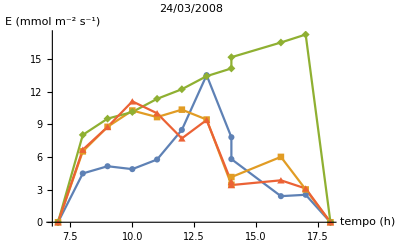

```mathematica
g1=ListLinePlot[{transpVsTempo120080324,transpVsTempo220080324,transpVsTempo320080324,transpVsTempo420080324},PlotLegend->{"-0.40MPa","-0.26MPa","-0.17MPa","-0.27MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Eucalipto - 24/03/2008 - PAR ( radiação fotossinteticamente ativa)

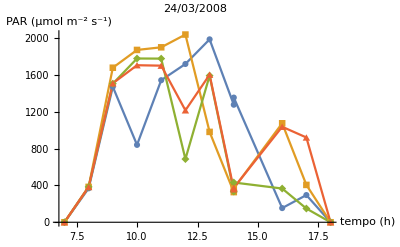

```mathematica
g2=ListLinePlot[{parVsTempo120080324,parVsTempo220080324,parVsTempo320080324,parVsTempo420080324},PlotLegend->{"-0.40MPa","-0.26MPa","-0.17MPa","-0.27MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Eucalipto - 24/03/2008 - DPV (déficit de pressão de vapor)

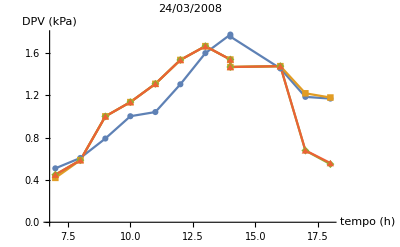

```mathematica
g3=ListLinePlot[{dpvVsTempo120080324,dpvVsTempo220080324,dpvVsTempo320080324,dpvVsTempo420080324},PlotLegend->{"-0.40MPa","-0.26MPa","-0.17MPa","-0.27MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Eucalipto - 24/03/2008 - Relação Transpiração - PAR

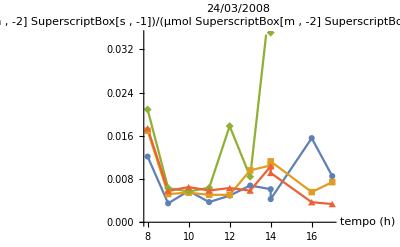

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120080324,transpSobrePARVsTempo220080324,transpSobrePARVsTempo320080324,transpSobrePARVsTempo420080324},PlotLegend->{"-0.40MPa","-0.26MPa","-0.17MPa","-0.27MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Eucalipto - 24/03/2008 - Relação Transpiração - DPV

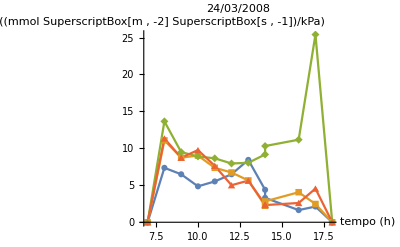

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120080324,transpSobreDPVVsTempo220080324,transpSobreDPVVsTempo320080324,transpSobreDPVVsTempo420080324},PlotLegend->{"-0.40MPa","-0.26MPa","-0.17MPa","-0.27MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```

## Parte 2

```mathematica
eucalipto120080325=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\1_20080325.xlsx"];
eucalipto220080325=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\2_20080325.xlsx"];
eucalipto320080325=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\3_20080325.xlsx"];
eucalipto420080325=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\4_20080325.xlsx"];
```

```mathematica
tempo=Table[eucalipto120080324[[1,i,1]],{i,1,Length[eucalipto120080324[[1]]]}];
```

```mathematica
transp120080325=Table[eucalipto120080325[[1,i,2]],{i,1,Length[tempo]}];
transp220080325=Table[eucalipto220080325[[1,i,2]],{i,1,Length[tempo]}];
transp320080325=Table[eucalipto320080325[[1,i,2]],{i,1,Length[tempo]}];
transp420080325=Table[eucalipto420080325[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120080325=Table[eucalipto120080325[[1,i,3]],{i,1,Length[tempo]}];
par220080325=Table[eucalipto220080325[[1,i,3]],{i,1,Length[tempo]}];
par320080325=Table[eucalipto320080325[[1,i,3]],{i,1,Length[tempo]}];
par420080325=Table[eucalipto420080325[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120080325=Table[eucalipto120080325[[1,i,4]],{i,1,Length[tempo]}];
dpv220080325=Table[eucalipto220080325[[1,i,4]],{i,1,Length[tempo]}];
dpv320080325=Table[eucalipto320080325[[1,i,4]],{i,1,Length[tempo]}];
dpv420080325=Table[eucalipto420080325[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120080325=N[Table[{tempo[[i]],transp120080325[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220080325=N[Table[{tempo[[i]],transp220080325[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320080325=N[Table[{tempo[[i]],transp320080325[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420080325=N[Table[{tempo[[i]],transp420080325[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120080325=N[Table[{tempo[[i]],par120080325[[i]]},{i,1,Length[tempo]}]];
parVsTempo220080325=N[Table[{tempo[[i]],par220080325[[i]]},{i,1,Length[tempo]}]];
parVsTempo320080325=N[Table[{tempo[[i]],par320080325[[i]]},{i,1,Length[tempo]}]];
parVsTempo420080325=N[Table[{tempo[[i]],par420080325[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120080325=N[Table[{tempo[[i]],dpv120080325[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220080325=N[Table[{tempo[[i]],dpv220080325[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320080325=N[Table[{tempo[[i]],dpv320080325[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420080325=N[Table[{tempo[[i]],dpv420080325[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120080325=Table[transp120080325[[i]]/par120080325[[i]],{i,1,Length[tempo]}];
transpSobrePAR220080325=Table[transp220080325[[i]]/par220080325[[i]],{i,1,Length[tempo]}];
transpSobrePAR320080325=Table[transp320080325[[i]]/par320080325[[i]],{i,1,Length[tempo]}];transpSobrePAR420080325=Table[transp420080325[[i]]/par420080325[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobrePARVsTempo120080325=N[Table[{tempo[[i]],transpSobrePAR120080325[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220080325=N[Table[{tempo[[i]],transpSobrePAR220080325[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320080325=N[Table[{tempo[[i]],transpSobrePAR320080325[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420080325=N[Table[{tempo[[i]],transpSobrePAR420080325[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120080325=Table[transp120080325[[i]]/dpv120080325[[i]],{i,1,Length[tempo]}];
transpSobreDPV220080325=Table[transp220080325[[i]]/dpv220080325[[i]],{i,1,Length[tempo]}];
transpSobreDPV320080325=Table[transp320080325[[i]]/dpv320080325[[i]],{i,1,Length[tempo]}];transpSobreDPV420080325=Table[transp420080325[[i]]/dpv420080325[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120080325=N[Table[{tempo[[i]],transpSobreDPV120080325[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220080325=N[Table[{tempo[[i]],transpSobreDPV220080325[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320080325=N[Table[{tempo[[i]],transpSobreDPV320080325[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420080325=N[Table[{tempo[[i]],transpSobreDPV420080325[[i]]},{i,1,Length[tempo]}]];
```

## Eucalipto - 25/03/2008 - Transpiração

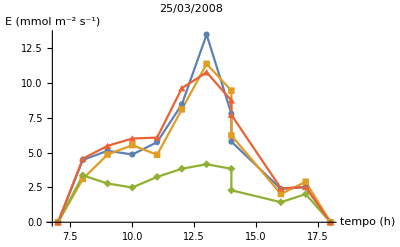

```mathematica
g1=ListLinePlot[{transpVsTempo120080325,transpVsTempo220080325,transpVsTempo320080325,transpVsTempo420080325},PlotLegend->{"-0.15MPa","-0.32MPa","-0.39MPa","-0.20MPa"},LegendPosition->{.7,-0.4},PlotLabel->"25/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Eucalipto - 25/03/2008 - PAR ( radiação fotossinteticamente ativa)

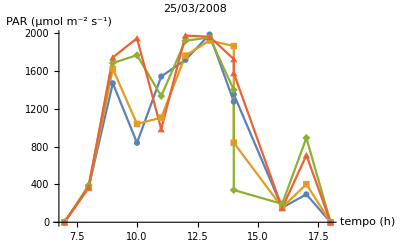

```mathematica
g2=ListLinePlot[{parVsTempo120080325,parVsTempo220080325,parVsTempo320080325,parVsTempo420080325},PlotLegend->{"-0.15MPa","-0.32MPa","-0.39MPa","-0.20MPa"},LegendPosition->{.7,-0.4},PlotLabel->"25/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Eucalipto - 25/03/2008 - DPV (déficit de pressão de vapor)

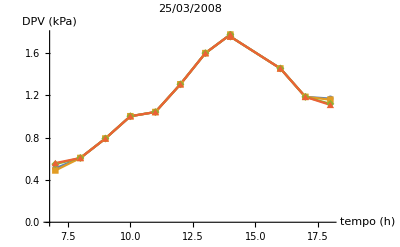

```mathematica
g3=ListLinePlot[{dpvVsTempo120080325,dpvVsTempo220080325,dpvVsTempo320080325,dpvVsTempo420080325},PlotLegend->{"-0.15MPa","-0.32MPa","-0.39MPa","-0.20MPa"},LegendPosition->{.7,-0.4},PlotLabel->"25/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Eucalipto - 25/03/2008 - Relação Transpiração - PAR

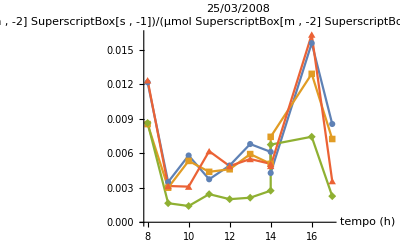

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120080325,transpSobrePARVsTempo220080325,transpSobrePARVsTempo320080325,transpSobrePARVsTempo420080325},PlotLegend->{"-0.15MPa","-0.32MPa","-0.39MPa","-0.20MPa"},LegendPosition->{.7,-0.4},PlotLabel->"25/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Eucalipto - 25/03/2008 - Relação Transpiração - DPV

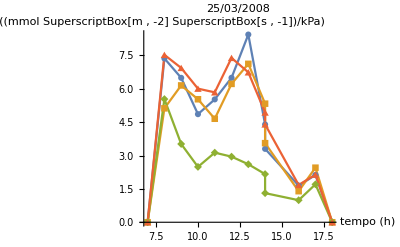

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120080325,transpSobreDPVVsTempo220080325,transpSobreDPVVsTempo320080325,transpSobreDPVVsTempo420080325},PlotLegend->{"-0.15MPa","-0.32MPa","-0.39MPa","-0.20MPa"},LegendPosition->{.7,-0.4},PlotLabel->"25/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```

## Parte 3

```mathematica
eucalipto120080617=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\1_20080617.xlsx"];
eucalipto220080617=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\2_20080617.xlsx"];
eucalipto320080617=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\3_20080617.xlsx"];
eucalipto420080617=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\eucalipto\\4_20080617.xlsx"];
```

```mathematica
tempo=Table[eucalipto120080617[[1,i,1]],{i,1,Length[eucalipto120080617[[1]]]}];
```

```mathematica
transp120080617=Table[eucalipto120080617[[1,i,2]],{i,1,Length[tempo]}];
transp220080617=Table[eucalipto220080617[[1,i,2]],{i,1,Length[tempo]}];
transp320080617=Table[eucalipto320080617[[1,i,2]],{i,1,Length[tempo]}];
transp420080617=Table[eucalipto420080617[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120080617=Table[eucalipto120080617[[1,i,3]],{i,1,Length[tempo]}];
par220080617=Table[eucalipto220080617[[1,i,3]],{i,1,Length[tempo]}];
par320080617=Table[eucalipto320080617[[1,i,3]],{i,1,Length[tempo]}];
par420080617=Table[eucalipto420080617[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120080617=Table[eucalipto120080617[[1,i,4]],{i,1,Length[tempo]}];
dpv220080617=Table[eucalipto220080617[[1,i,4]],{i,1,Length[tempo]}];
dpv320080617=Table[eucalipto320080617[[1,i,4]],{i,1,Length[tempo]}];
dpv420080617=Table[eucalipto420080617[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120080617=N[Table[{tempo[[i]],transp120080617[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220080617=N[Table[{tempo[[i]],transp220080617[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320080617=N[Table[{tempo[[i]],transp320080617[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420080617=N[Table[{tempo[[i]],transp420080617[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120080617=N[Table[{tempo[[i]],par120080617[[i]]},{i,1,Length[tempo]}]];
parVsTempo220080617=N[Table[{tempo[[i]],par220080617[[i]]},{i,1,Length[tempo]}]];
parVsTempo320080617=N[Table[{tempo[[i]],par320080617[[i]]},{i,1,Length[tempo]}]];
parVsTempo420080617=N[Table[{tempo[[i]],par420080617[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120080617=N[Table[{tempo[[i]],dpv120080617[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220080617=N[Table[{tempo[[i]],dpv220080617[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320080617=N[Table[{tempo[[i]],dpv320080617[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420080617=N[Table[{tempo[[i]],dpv420080617[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120080617=Table[transp120080617[[i]]/par120080617[[i]],{i,1,Length[tempo]}];
transpSobrePAR220080617=Table[transp220080617[[i]]/par220080617[[i]],{i,1,Length[tempo]}];
transpSobrePAR320080617=Table[transp320080617[[i]]/par320080617[[i]],{i,1,Length[tempo]}];transpSobrePAR420080617=Table[transp420080617[[i]]/par420080617[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobrePARVsTempo120080617=N[Table[{tempo[[i]],transpSobrePAR120080617[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220080617=N[Table[{tempo[[i]],transpSobrePAR220080617[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320080617=N[Table[{tempo[[i]],transpSobrePAR320080617[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420080617=N[Table[{tempo[[i]],transpSobrePAR420080617[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120080617=Table[transp120080617[[i]]/dpv120080617[[i]],{i,1,Length[tempo]}];
transpSobreDPV220080617=Table[transp220080617[[i]]/dpv220080617[[i]],{i,1,Length[tempo]}];
transpSobreDPV320080617=Table[transp320080617[[i]]/dpv320080617[[i]],{i,1,Length[tempo]}];transpSobreDPV420080617=Table[transp420080617[[i]]/dpv420080617[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120080617=N[Table[{tempo[[i]],transpSobreDPV120080617[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220080617=N[Table[{tempo[[i]],transpSobreDPV220080617[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320080617=N[Table[{tempo[[i]],transpSobreDPV320080617[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420080617=N[Table[{tempo[[i]],transpSobreDPV420080617[[i]]},{i,1,Length[tempo]}]];
```

## Eucalipto - 17/06/2008 - Transpiração

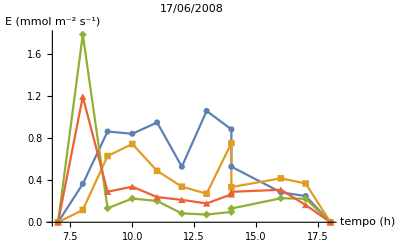

```mathematica
g1=ListLinePlot[{transpVsTempo120080617,transpVsTempo220080617,transpVsTempo320080617,transpVsTempo420080617},PlotLegend->{"-1.06MPa","-0.26MPa","-1.87MPa","-2.47MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/06/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Eucalipto - 17/06/2008 - PAR ( radiação fotossinteticamente ativa)

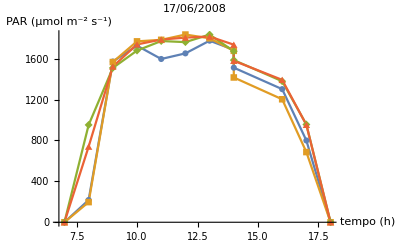

```mathematica
g2=ListLinePlot[{parVsTempo120080617,parVsTempo220080617,parVsTempo320080617,parVsTempo420080617},PlotLegend->{"-1.06MPa","-0.26MPa","-1.87MPa","-2.47MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/06/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Eucalipto - 17/06/2008 - DPV (déficit de pressão de vapor)

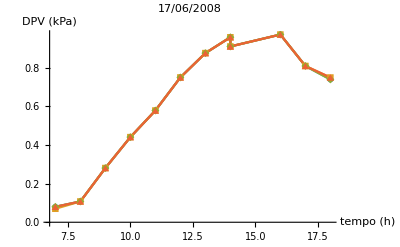

```mathematica
g3=ListLinePlot[{dpvVsTempo120080617,dpvVsTempo220080617,dpvVsTempo320080617,dpvVsTempo420080617},PlotLegend->{"-1.06MPa","-0.26MPa","-1.87MPa","-2.47MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/06/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Eucalipto - 17/06/2008 - Relação Transpiração - PAR

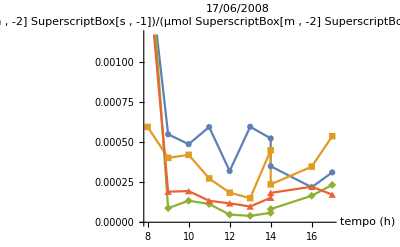

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120080617,transpSobrePARVsTempo220080617,transpSobrePARVsTempo320080617,transpSobrePARVsTempo420080617},PlotLegend->{"-1.06MPa","-0.26MPa","-1.87MPa","-2.47MPa"},LegendPosition->{.7,-0.4},PlotLabel->"17/06/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Eucalipto - 17/06/2008 - Relação Transpiração - DPV

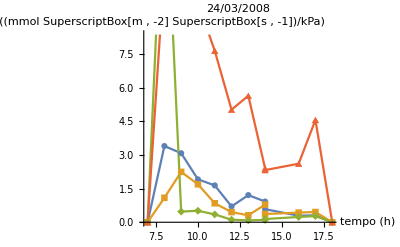

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120080617,transpSobreDPVVsTempo220080617,transpSobreDPVVsTempo320080617,transpSobreDPVVsTempo420080324},PlotLegend->{"-1.06MPa","-0.26MPa","-1.87MPa","-2.47MPa"},LegendPosition->{.7,-0.4},PlotLabel->"24/03/2008",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```